# Homework 7 Statiscal Mechanics

## U2x2

```mathematica
α:=E^((I π)/4)ν
```

```mathematica
o:=ConstantArray[0,{4,4}]
i:=IdentityMatrix[4]
r:={{ν,α,0,α*},{0,0,0,0},{0,0,0,0},{0,0,0,0}}
l:={{0,0,0,0},{0,0,0,0},{0,α*,ν,α},{0,0,0,0}}
u:={{0,0,0,0},{α*,ν,α,0},{0,0,0,0},{0,0,0,0}}
d:={{0,0,0,0},{0,0,0,0},{0,0,0,0},{α,0,α*,ν}}
```

```mathematica
U:=ArrayFlatten[{{i,r,u,o},{l,i,o,u},{d,o,i,r},{o,d,l,i}}]
```

```mathematica
Refine[MatrixForm[U],ν∈Reals]
```

(1 | 0 | 0 | 0 | ν | ⅇ^((ⅈ π)/4) ν | 0 | ⅇ^(-(ⅈ π)/4) ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) ν | ν | ⅇ^((ⅈ π)/4) ν | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) ν | ν | ⅇ^((ⅈ π)/4) ν | 0
0 | ⅇ^(-(ⅈ π)/4) ν | ν | ⅇ^((ⅈ π)/4) ν | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | ν | ⅇ^((ⅈ π)/4) ν | 0 | ⅇ^(-(ⅈ π)/4) ν
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
ⅇ^((ⅈ π)/4) ν | 0 | ⅇ^(-(ⅈ π)/4) ν | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅇ^(-(ⅈ π)/4) ν | ν | ⅇ^((ⅈ π)/4) ν | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | ⅇ^((ⅈ π)/4) ν | 0 | ⅇ^(-(ⅈ π)/4) ν | ν | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Refine[Det[U],ν∈Reals]
```

(1+ν^4)^2

## Kac-Ward 4x4

```mathematica
Clear[U]
```

```mathematica
δ:=ArrayFlatten[{
{o,r,o,o,u,o,o,o,o,o,o,o,o,o,o,o},
{l,o,r,o,o,u,o,o,o,o,o,o,o,o,o,o},
{o,l,o,r,o,o,u,o,o,o,o,o,o,o,o,o},
{o,o,l,o,o,o,o,u,o,o,o,o,o,o,o,o},
{d,o,o,o,o,r,o,o,u,o,o,o,o,o,o,o},
{o,d,o,o,l,o,r,o,o,u,o,o,o,o,o,o},
{o,o,d,o,o,l,o,r,o,o,u,o,o,o,o,o},
{o,o,o,d,o,o,l,o,o,o,o,u,o,o,o,o},
{o,o,o,o,d,o,o,o,o,r,o,o,u,o,o,o},
{o,o,o,o,o,d,o,o,l,o,r,o,o,u,o,o},
{o,o,o,o,o,o,d,o,o,l,o,r,o,o,u,o},
{o,o,o,o,o,o,o,d,o,o,l,o,o,o,o,u},
{o,o,o,o,o,o,o,o,d,o,o,o,o,r,o,o},
{o,o,o,o,o,o,o,o,o,d,o,o,l,o,r,o},
{o,o,o,o,o,o,o,o,o,o,d,o,o,l,o,r},
{o,o,o,o,o,o,o,o,o,o,o,d,o,o,l,o}
}]
```

```mathematica
U:=Refine[IdentityMatrix[4*2^4]+δ,ν∈Reals]
```

```mathematica
Det[U]
```

1+18 ν^4+24 ν^6+181 ν^8+400 ν^10+1360 ν^12+3088 ν^14+7690 ν^16+15088 ν^18+28292 ν^20+42400 ν^22+53322 ν^24+49776 ν^26+36096 ν^28+17456 ν^30+6005 ν^32+784 ν^34+154 ν^36+8 ν^38+ν^40

```mathematica
Factor[%]
```

(1+9 ν^4+12 ν^6+50 ν^8+92 ν^10+158 ν^12+116 ν^14+69 ν^16+4 ν^18+ν^20)^2

```mathematica
Z=Simplify[Cosh[β]^16 Sqrt[Det[U]]/.ν-> Tanh[β],β>0]
```

Cosh[β]^16 (1+9 Tanh[β]^4+12 Tanh[β]^6+50 Tanh[β]^8+92 Tanh[β]^10+158 Tanh[β]^12+116 Tanh[β]^14+69 Tanh[β]^16+4 Tanh[β]^18+Tanh[β]^20)

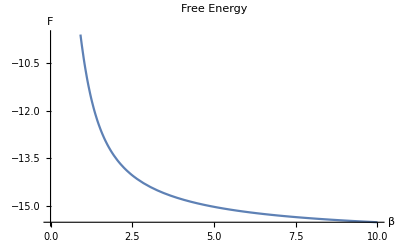

```mathematica
Plot[-1/β Log[Z],{β,0,10},AxesLabel->{HoldForm[β],HoldForm[F]},PlotLabel->HoldForm[Free Energy],LabelStyle->{GrayLevel[0]}]
```